```mathematica
(*Using Zhu, Xiong paper*)
(* Distance between nuclei*)

(**)

(* L equation and coefficients *)
σ[r_]:=r/p-1/2;
α[n_]:=(n+1)(n+1/2);
β[n_,r_]:=2 n^2+(4p-2σ[r])n-A +p^2-2p σ[r]-σ[r]/2;
γ[n_,r_]:=(n-1)(n-2σ[r]-1/2)+σ[r](σ[r]-1/2);

(* Create a continued fraction equation for the coefficients of L equation *)

lCoeff2[n_,r_]:=β[0,r]/α[0]+Simplify[ContinuedFractionK[-α[i-1]γ[i,r],β[i,r],{i,1,n}]] ;

(* M equation and coefficients *)

w=-A +p^2/2;      q= -p^2/4;
v[n_]:=Simplify[(w-n^2)/q];
(* Evaluate as a continued fraction *)
mCoeffV0[n_]:=v[0]+2Simplify[ContinuedFractionK[-1,v[2i],{i,1,n}]];

mCoeffV1[n_]:=v[1]-1+Simplify[ContinuedFractionK[-1,v[2i+1],{i,1,n}]];

(* Parameters:
n: Depth of the continued fraction,
 R: Internuclear distance,
 gerade: flag indicating whether we are calculating gerade or ungerade states
output:
R , electron energy, total energy, separation constant, and p value 
*)
energySingleR[n_,R_, gerade_]:=
Module[{asAndps,pe,energy,aa},
(*Now find p and A *)
If[gerade==1, 
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV0[n]==0},{A,p},Reals],
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV1[n]==0},{A,p},Reals]];
aa=Sort[asAndps[[All,1,2]], Greater][[1]];
pe=Sort[asAndps[[All,2,2]], Greater][[1]];
energy = (-2)/R^2 pe^2;
{R,energy, energy + 1/R,aa,pe}
]
allRs = Table[0.2+i*0.1,{i,0,9}];
allRs = Join[allRs, Table[1+.5*i,{i,1,8}]];
allRs = Join[allRs, Table[5+i,{i,1,45}]];

energiesGerade = Map[energySingleR[6,#1,1] &, allRs];
energiesUngerade = Map[energySingleR[6,#1,2] &, allRs];
Prepend[energiesGerade, {"R", "E", "E+1/r", "A", "p"}]  //MatrixForm
Export["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx",energiesGerade, "mx"];
Prepend[energiesUngerade, {"R", "E","E+1/r", "A", "p"}]  //MatrixForm
Export["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx",energiesUngerade, "mx"];
```

(R | E | E+1/r | A | p
0.2 | -6.50361 | -1.50361 | 19.2757 | 0.360655
0.3 | -5.81983 | -2.48649 | 175.774 | 0.511754
0.4 | -5.27552 | -2.77552 | 198.466 | 0.649647
0.5 | -4.83822 | -2.83822 | 218.834 | 0.777674
0.6 | -4.48148 | -2.81482 | 30.6031 | 0.898146
0.7 | -4.18616 | -2.75759 | 255.124 | 1.01272
0.8 | -3.93852 | -2.68852 | 271.721 | 1.12264
0.9 | -3.72861 | -2.6175 | 287.554 | 1.22886
1. | -3.54905 | -2.54905 | 302.754 | 1.33211
1.1 | -3.39429 | -2.4852 | 317.417 | 1.43302
1.5 | -2.95083 | -2.28416 | 371.99 | 1.822
2. | -2.63638 | -2.13638 | 433.864 | 2.29625
2.5 | -2.4621 | -2.0621 | 491.12 | 2.77382
3. | -2.36086 | -2.02752 | 545.139 | 3.25943
3.5 | -2.29797 | -2.01225 | 596.728 | 3.75167
4. | -2.25565 | -2.00565 | 646.407 | 4.24796
4.5 | -2.22496 | -2.00274 | 694.536 | 4.74634
5. | -2.20134 | -2.00134 | 741.373 | 5.24564
6 | -2.16637 | -1.9997 | 16608. | 6.24457
7 | -2.14043 | -1.99757 | 919.107 | 7.24158
8 | -2.11874 | -1.99374 | 1003.68 | 8.23405
9 | -2.09856 | -1.98745 | 1086.12 | 9.21909
10 | -2.07822 | -1.97822 | 1166.79 | 10.1937
11 | -2.05677 | -1.96586 | 17104.9 | 11.155
12 | -2.03377 | -1.95044 | 1323.77 | 12.1009
13 | -2.00914 | -1.93221 | 1400.47 | 13.0297
14 | -1.98298 | -1.91155 | 1476.16 | 13.9403
15 | -1.95552 | -1.88886 | 1550.94 | 14.8323
16 | -1.92706 | -1.86456 | 1624.9 | 15.7055
17 | -1.89785 | -1.83903 | 17692.3 | 16.5602
18 | -1.86817 | -1.81261 | 17789.3 | 17.3967
19 | -1.83825 | -1.78562 | 17886. | 18.2155
20 | -1.80829 | -1.75829 | 17982.6 | 19.0173
21 | -1.77845 | -1.73083 | 18078.9 | 19.8027
22 | -1.74887 | -1.70341 | 2055.23 | 20.5725
23 | -1.71965 | -1.67618 | 18270.8 | 21.3272
24 | -1.69089 | -1.64922 | 2194.63 | 22.0675
25 | -1.66264 | -1.62264 | 2263.72 | 22.7942
26 | -1.63495 | -1.59649 | 2332.43 | 23.5077
27 | -1.60785 | -1.57082 | 2400.8 | 24.2087
28 | -1.58138 | -1.54566 | 2468.83 | 24.8978
29 | -1.55553 | -1.52105 | 2536.55 | 25.5754
30 | -1.53032 | -1.49699 | 2603.97 | 26.242
31 | -1.50575 | -1.47349 | 19029.7 | 26.8982
32 | -1.48182 | -1.45057 | 19123.6 | 27.5443
33 | -1.45851 | -1.42821 | 19217.4 | 28.1808
34 | -1.43582 | -1.40641 | 19310.9 | 28.8081
35 | -1.41374 | -1.38517 | 2937.08 | 29.4265
36 | -1.39225 | -1.36448 | 3002.99 | 30.0363
37 | -1.37134 | -1.34432 | 3068.68 | 30.638
38 | -1.351 | -1.32468 | 19683.2 | 31.2317
39 | -1.3312 | -1.30555 | 3199.46 | 31.8178
40 | -1.31193 | -1.28693 | 3264.56 | 32.3966
41 | -1.29317 | -1.26878 | 3329.48 | 32.9683
42 | -1.27492 | -1.25111 | 20052.6 | 33.5332
43 | -1.25714 | -1.23389 | 3458.79 | 34.0915
44 | -1.23984 | -1.21711 | 3523.19 | 34.6434
45 | -1.22298 | -1.20076 | 20327.8 | 35.1891
46 | -1.20656 | -1.18483 | 20419.2 | 35.7288
47 | -1.19057 | -1.16929 | 3715.48 | 36.2627
48 | -1.17498 | -1.15415 | 3779.29 | 36.791
49 | -1.15979 | -1.13938 | 3842.95 | 37.3139
50 | -1.14498 | -1.12498 | 3906.48 | 37.8315)

(R | E | E+1/r | A | p
0.2 | -0.841481 | 4.15852 | 33.4451 | 0.129729
0.3 | -0.911818 | 2.42152 | 39.6245 | 0.202563
0.4 | -1.03317 | 1.46683 | 44.6816 | 0.287495
0.5 | -1.20111 | 0.798885 | 49.0907 | 0.387478
0.6 | -1.39266 | 0.274004 | 53.0632 | 0.500679
0.7 | -1.58212 | -0.153551 | 56.7159 | 0.622591
0.8 | -1.75267 | -0.502667 | 395.73 | 0.748901
0.9 | -1.89725 | -0.786142 | 417.783 | 0.876577
1. | -2.01521 | -1.01521 | 66.3746 | 1.0038
1.1 | -2.10899 | -1.1999 | 459.254 | 1.12957
1.5 | -2.31161 | -1.64494 | 534.677 | 1.61262
2. | -2.36744 | -1.86744 | 619.719 | 2.17598
2.5 | -2.35029 | -1.95029 | 698.046 | 2.7101
3. | -2.31526 | -1.98193 | 111.724 | 3.2278
3.5 | -2.2797 | -1.99399 | 841.77 | 3.73673
4. | -2.24845 | -1.99845 | 909.103 | 4.24118
4.5 | -2.22222 | -2. | 974.188 | 4.74341
5. | -2.20044 | -2.00044 | 1037.4 | 5.24457
6 | -2.16704 | -2.00038 | 1159.29 | 6.24554
7 | -2.14278 | -1.99992 | 1276.36 | 7.24556
8 | -2.12404 | -1.99904 | 1389.63 | 8.24435
9 | -2.10851 | -1.9974 | 1499.83 | 9.24093
10 | -2.09461 | -1.99461 | 1607.45 | 10.2338
11 | -2.08121 | -1.9903 | 1712.89 | 11.2211
12 | -2.06756 | -1.98423 | 1816.44 | 12.201
13 | -2.05313 | -1.97621 | 1918.34 | 13.1715
14 | -2.03763 | -1.96621 | 2018.78 | 14.1311
15 | -2.02093 | -1.95427 | 2117.92 | 15.0783
16 | -2.00302 | -1.94052 | 2215.89 | 16.0121
17 | -1.98395 | -1.92512 | 2312.8 | 16.9316
18 | -1.96385 | -1.90829 | 2408.73 | 17.8366
19 | -1.94287 | -1.89023 | 2503.78 | 18.7266
20 | -1.92115 | -1.87115 | 2598.02 | 19.6018
21 | -1.89886 | -1.85124 | 2691.5 | 20.4621
22 | -1.87614 | -1.83069 | 2784.28 | 21.3079
23 | -1.85312 | -1.80965 | 2876.4 | 22.1394
24 | -1.82993 | -1.78826 | 2967.92 | 22.9569
25 | -1.80666 | -1.76666 | 3058.86 | 23.7609
26 | -1.7834 | -1.74494 | 3149.27 | 24.5518
27 | -1.76024 | -1.7232 | 3239.17 | 25.33
28 | -1.73723 | -1.70152 | 3328.59 | 26.0959
29 | -1.71444 | -1.67995 | 3417.56 | 26.85
30 | -1.69189 | -1.65856 | 3506.1 | 27.5926
31 | -1.66964 | -1.63738 | 3594.23 | 28.3243
32 | -1.64771 | -1.61646 | 3681.98 | 29.0453
33 | -1.62612 | -1.59582 | 3769.36 | 29.756
34 | -1.60489 | -1.57548 | 3856.38 | 30.4569
35 | -1.58403 | -1.55546 | 3943.07 | 31.1483
36 | -1.56355 | -1.53577 | 4029.44 | 31.8305
37 | -1.54345 | -1.51643 | 4115.49 | 32.5038
38 | -1.52375 | -1.49743 | 4201.26 | 33.1685
39 | -1.50444 | -1.4788 | 4286.73 | 33.8249
40 | -1.48551 | -1.46051 | 4371.94 | 34.4733
41 | -1.46698 | -1.44259 | 4456.88 | 35.114
42 | -1.44882 | -1.42501 | 4541.56 | 35.7472
43 | -1.43105 | -1.40779 | 4626.01 | 36.3732
44 | -1.41365 | -1.39092 | 4710.21 | 36.9921
45 | -1.39662 | -1.37439 | 4794.19 | 37.6042
46 | -1.37994 | -1.3582 | 4877.95 | 38.2097
47 | -1.36362 | -1.34235 | 4961.5 | 38.8088
48 | -1.34765 | -1.32682 | 5044.84 | 39.4017
49 | -1.33201 | -1.31161 | 1540.71 | 39.9885
50 | -1.31671 | -1.29671 | 1586.09 | 40.5695)

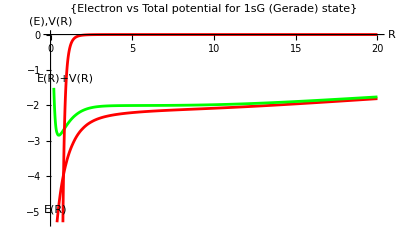

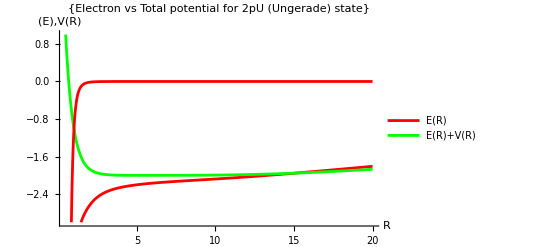

```mathematica
eG = Interpolation[Transpose[{energiesGerade[[All,1]],energiesGerade[[All,2]]}]];
eGTotal = Interpolation[Transpose[{energiesGerade[[All,1]],energiesGerade[[All,3]]}]];

Plot[{eG[x],eGTotal[x], -1/x^6},{x,0.2,20}, PlotStyle->{Red,Green}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 1sG (Gerade) state"}, PlotLabels->Placed[{"E(R)","E(R)+V(R)"},{Left}], PlotRange->Automatic]

eU = Interpolation[Transpose[{energiesUngerade[[All,1]],energiesGerade[[All,2]]}]];
eUTotal = Interpolation[Transpose[{energiesUngerade[[All,1]],energiesUngerade[[All,3]]}]];

Plot[{eU[x],eUTotal[x],-1/x^6},{x,0.2,20}, PlotStyle->{Red,Green},PlotRange->{1,-3}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 2pU (Ungerade) state"}, PlotLegends->{"E(R)","E(R)+V(R)"}]
```